```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\GitHub\VM2D\settings\airfoils

```mathematica
β=9.5;
ρ=0.015;
```

```mathematica
t=1.0;
```

```mathematica
c=t β
```

9.5

```mathematica
n=100;
```

```mathematica
L=1/n;
```

```mathematica
nc=Ceiling[(c-2ρ)/L]
```

948

```mathematica
nt=If[OddQ[#],#+1,#]&@Ceiling[(t-2ρ)/L]
```

98

```mathematica
nr=If[OddQ[#],#+1,#]&@Ceiling[(2π ρ)/(4 L)]
```

4

```mathematica
PtsA=N[Table[{(c/2-ρ)+ρ Cos[(2π)/(4nr)(i-1.0)],(t/2-ρ)+ρ Sin[(2π)/(4nr)(i-1.0)]},{i,1,nr}],16]
```

{{4.75,0.485},{4.74886,0.49074},{4.74561,0.495607},{4.74074,0.498858}}

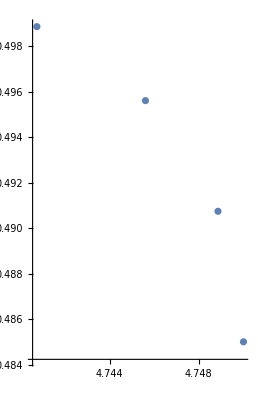

```mathematica
ListPlot[PtsA,AspectRatio->Automatic]
```

```mathematica
PtsB=Table[{c/2-ρ-(c-2ρ)/nc(i-1),t/2},{i,1,nc}];
```

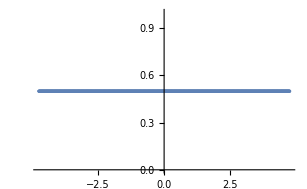

```mathematica
ListPlot[PtsB]
```

```mathematica
PtsC=N[Table[{-(c/2-ρ)+ρ Cos[π/2+(2π)/(4nr)(i-1.0)],(t/2-ρ)+ρ Sin[π/2+(2π)/(4nr)(i-1.0)]},{i,1,nr}],16]
```

{{-4.735,0.5},{-4.74074,0.498858},{-4.74561,0.495607},{-4.74886,0.49074}}

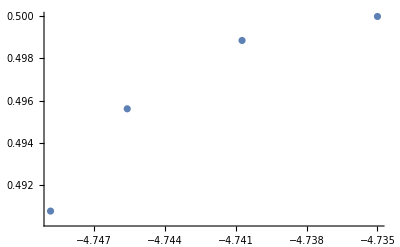

```mathematica
ListPlot[PtsC]
```

```mathematica
PtsD=Table[{(-c)/2,t/2-ρ-((t-2ρ)/nt)(i-1)},{i,1,nt}];
```

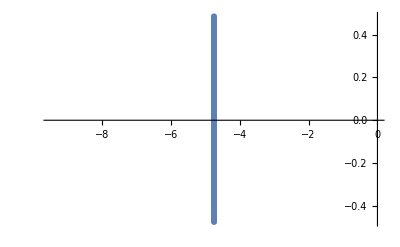

```mathematica
ListPlot[PtsD]
```

```mathematica
PtsE=N[Table[{-(c/2-ρ)+ρ Cos[(2π)/2+(2π)/(4nr)(i-1.0)],(-t/2+ρ)+ρ Sin[(2π)/2+(2π)/(4nr)(i-1.0)]},{i,1,nr}],16];
```

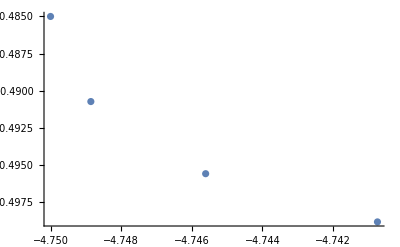

```mathematica
ListPlot[PtsE]
```

```mathematica
PtsF=Table[{-c/2+ρ+(c-2ρ)/nc(i-1),-t/2},{i,1,nc}];
```

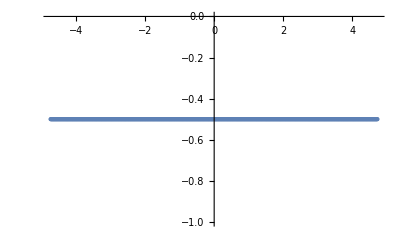

```mathematica
ListPlot[PtsF]
```

```mathematica
PtsG=N[Table[{(c/2-ρ)+ρ Cos[(3π)/2+(2π)/(4nr)(i-1.0)],(-t/2+ρ)+ρ Sin[(3π)/2+(2π)/(4nr)(i-1.0)]},{i,1,nr}],16];
```

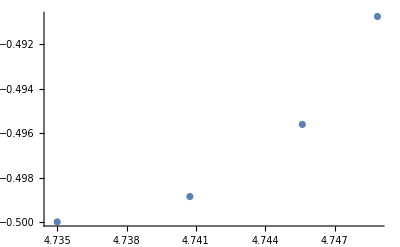

```mathematica
ListPlot[PtsG]
```

```mathematica
PtsH=Table[{c/2,-t/2+ρ+(t-2ρ)/nt(i-1)},{i,1,nt}];
```

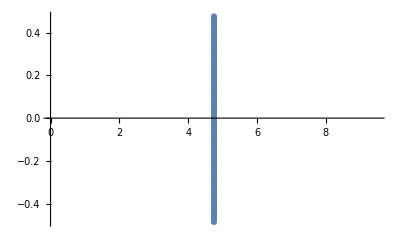

```mathematica
ListPlot[PtsH]
```

```mathematica
Pts=RotateRight[Join[PtsA,PtsB,PtsC,PtsD,PtsE,PtsF,PtsG,PtsH],nt/2]
```

{{4.75,-5.55112×10^-17},{4.75,0.00989796},{4.75,0.0197959},{4.75,0.0296939},{4.75,0.0395918},{4.75,0.0494898},{4.75,0.0593878},{4.75,0.0692857},{4.75,0.0791837},{4.75,0.0890816},2088,{4.75,-0.0989796},{4.75,-0.0890816},{4.75,-0.0791837},{4.75,-0.0692857},{4.75,-0.0593878},{4.75,-0.0494898},{4.75,-0.0395918},{4.75,-0.0296939},{4.75,-0.0197959},{4.75,-0.00989796}}
 |  |  |  |

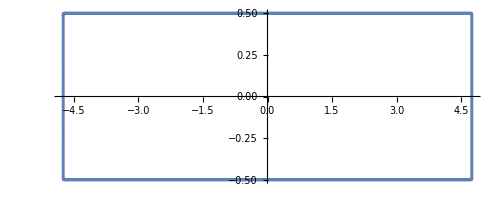

```mathematica
ListPlot[Pts,AspectRatio->Automatic]
```

```mathematica
Length@Pts
```

2108

```mathematica
Export["roundedRect"<>ToString[β]<>"np"<>ToString[Length@Pts],
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.10   |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2021/05/21     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2021 Ilia Marchevsky, Kseniia Sokol, Evgeniya Ryatina    |
*-----------------------------------------------------------------------------*
| File name: roundedRect"<>ToString[β]<>"np"<>ToString[Length@Pts]<>StringRepeat[" ",51-StringLength@ToString[Length@Pts]]<>"|
| Info: Rounded rectangle airfoil, "<>ToString[β]<>" elong, ("<>TextString[Length@Pts]<>" panels)"<>StringRepeat[" ",25-StringLength@ToString[Length@Pts]]<>"|
\\*---------------------------------------------------------------------------*/
"}~Join~{"r = {"}~Join~((TextString[#]<>",")&/@(Pts[[1;;-2]]))~Join~((TextString[#])&/@(Pts[[{-1}]]))~Join~{" };"},"Table"]
```

roundedRect9.5np2108